# 3Q states on the triangular lattice

## Visualization

## Lattice

Triangular lattice

```mathematica
a ={{1,0},{1/2,(√3)/2}} ;
b =2π{{1,-1/(√3)},{0,2/(√3)}} ;
Array[ a[[#1]].b[[#2]]&,{2,2}]//MatrixForm
```

(2 π | 0
0 | 2 π)

```mathematica
r[i_,j_]:=i a[[1]] + j a[[2]];
g[i_,j_]:=i b[[1]] + j b[[2]];
```

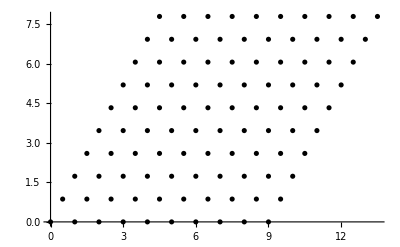

```mathematica
nsites=10;
lattice=ArrayFlatten[ Table[ r[i,j],{i,0,nsites-1},{j,0,nsites-1}],1];
lat= ListPlot[lattice,PlotStyle->Black]
```

## 3D

GFX objects

```mathematica
sphere[pos_,r_]:=Graphics3D[{Opacity[0.1],Specularity[White,1],Black,Sphere[{pos[[1]],pos[[2]],0},r]}]
```

```mathematica
cylinder[pos1_,pos2_,r_]:=Graphics3D[{Opacity[0.1],Specularity[White,1],Black,Cylinder[{{pos1[[1]],pos1[[2]],0},{pos2[[1]],pos2[[2]],0}},r]}]
```

```mathematica
objs={};
radius = 0.1;
For[i=1,i≤ nsites, i++, {
For[j=1,j≤ nsites, j++, {
pos = r[i,j];
objs = objs ~ Join ~{ sphere[pos,radius]};

If[i<nsites, {
posA  = r[i+1,j];
objs = objs ~ Join ~{ cylinder[pos,posA,radius/3]};
}];
If[j<nsites, {
posA  = r[i,j+1];
objs = objs ~ Join ~{ cylinder[pos,posA,radius/3]};
}];
If[i<nsites && j<nsites, {
posA  = r[i+1,j];
posB  = r[i,j+1];
objs = objs ~ Join ~{ cylinder[posA,posB,radius/3]};
}];
}
];
}];
Show[objs]
```

-Graphics3D-

## Skyrmion triple-Q

Q vectors

```mathematica
q[1] =  g[0,1] ;
q[2] = RotationMatrix[2 π/3].q[1];
q[3] = RotationMatrix[4 π/3].q[1];
```

Theta matrix

```mathematica
(   {i,j}/.Solve[q[#]==i b[[1]] + j b[[2]] , {i,j} ][[1]]  )& /@ Range[3] //MatrixForm
```

(0 | 1
-1 | -1
1 | 0)

```mathematica
b[[1]]
```

{2 π,-(2 π)/(√3)}

Phase variables

```mathematica
Ψsk=0;
ψsk[1] = Ψsk;
ψsk[2] = Ψsk+π;
ψsk[3] = Ψsk;

ϕsk[i1_,i2_,k_]:=θsk r[i1,i2].q[k] +ψsk[k]
```

```mathematica
ϕsk[i1,i2,1]+ϕsk[i1,i2,2]+ϕsk[i1,i2,3] // FullSimplify
```

π

```mathematica
nsites=50;
θsk=1/nsites;

hull = ArrayFlatten[Table[ { Mod[ϕsk[i1,i2,1],2π],Mod[ϕsk[i1,i2,2],2π]},{i1,0,nsites-1},{i2,0,nsites-1}],1];
```

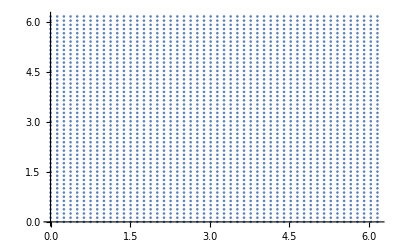

```mathematica
ListPlot[hull]
```

Skyrmion lattice

```mathematica
nsk[i1_,i2_,k_]:= { 0,  Sin[ ϕsk[i1,i2,k]],Cos[ ϕsk[i1,i2,k]]};
Rot[k_]:=RotationMatrix[(k-1)2π/3,{0,0,1}];



nsk [i1_,i2_]:= Normalize[ Sum[Rot[k].nsk[i1,i2,k],{k,1,3}]]//N;
```

```mathematica
cmap=ColorData["RedBlueTones"];
```

```mathematica
spinsk[i1_,i2_,radius_,head_]:=(
pos = r[i1,i2]~Join~{0};
vec = nsk[i1,i2];
pA = pos-1/2vec;
pB = pos+1/2vec;
Return[Graphics3D[{cmap[Rescale[vec[[3]],{-1,1}]],Lighting-> "Neutral",Arrowheads[head],Arrow[Tube[{pA,pB},radius]]}]];
);
```

```mathematica
objs={};

extent=20;
radius = 0.2;
nsites=extent;
θsk=3/nsites;
For[i=0,i≤  nsites, i++, {
For[j=0,j≤ nsites, j++, {
pos = r[i,j];
If[True, {
objs = objs ~ Join ~{ spinsk[i,j,0.05,0.02]};
(*objs = objs ~ Join ~{ sphere[pos,radius]};*)

If[i<nsites, {
posA  = r[i+1,j];
objs = objs ~ Join ~{ cylinder[pos,posA,radius/3]};
}];
If[j<nsites, {
posA  = r[i,j+1];
objs = objs ~ Join ~{ cylinder[pos,posA,radius/3]};
}];
If[i<nsites && j<nsites, {
posA  = r[i+1,j];
posB  = r[i,j+1];
objs = objs ~ Join ~{ cylinder[posA,posB,radius/3]};
}];

}];
}
];
}];
```

```mathematica
Show[objs,ImageSize-> 1000,ViewPoint->{0,0.1,2},ViewCenter-> {0.5,0.5,0},Boxed-> False]
```

-Graphics3D-

## SDW triple-Q

Q vectors

```mathematica
q[1] =  g[0,1] ;
q[2] = RotationMatrix[2 π/3].q[1];
q[3] = RotationMatrix[4 π/3].q[1];
```

Phase variables

```mathematica
Ψsdw=0;
ψsdw[1] = Ψsdw;
ψsdw[2] = Ψsdw+π;
ψsdw[3] = Ψsdw;

ϕsdw[i1_,i2_,k_]:=θsdw r[i1,i2].q[k] +ψsdw[k]
```

```mathematica
ϕsdw[i1,i2,1]+ ϕsdw[i1,i2,2]+ ϕsdw[i1,i2,3] // FullSimplify
```

π

```mathematica
nsites=50;
θsdw=1/nsites;

hull = ArrayFlatten[Table[ { Mod[ϕsdw[i1,i2,1],2π],Mod[ϕsdw[i1,i2,2],2π]},{i1,0,nsites-1},{i2,0,nsites-1}],1];
```

```mathematica
ListPlot[hull]
```

-Graphics-

Skyrmion lattice

```mathematica
nsdw[i1_,i2_,k_]:= {  Sin[ ϕsdw[i1,i2,k]],0,0};
Rot[k_]:=RotationMatrix[(k-1)2π/3,{0,0,1}];



nsdw[i1_,i2_]:= Sum[Rot[k].nsdw[i1,i2,k],{k,1,3}] /3 //N
```

```mathematica
extent=15;
radius = 0.2;
nsites=extent;
θsdw=3/nsites;
```

```mathematica
vecnorm = Table[ Norm[nsdw[i,j]] ,{i,0,nsites},{j,0,nsites} ] //Flatten//Max
```

0.583002

```mathematica
cmap=ColorData["RedBlueTones"];
```

```mathematica
spinsdw[i1_,i2_,radius_,head_]:=(
pos = r[i1,i2]~Join~{0};
vec = Normalize[nsdw[i1,i2]];
s = Norm[nsdw[i1,i2]]/vecnorm;
pA = pos-1/2vec;
pB = pos+1/2vec;
Return[Graphics3D[Scale[{cmap[Rescale[vec[[1]],{-1,1}]],Lighting-> "Neutral",Arrowheads[head],Arrow[Tube[{pA,pB},radius]]},s]]];
);
```

```mathematica
objs={};

extent=20;
radius = 0.2;
nsites=extent;
θsdw=3/nsites;
For[i=0,i≤  nsites, i++, {
For[j=0,j≤ nsites, j++, {
pos = r[i,j];
If[True, {
objs = objs ~ Join ~{ spinsdw[i,j,0.05,0.02]};
(*objs = objs ~ Join ~{ sphere[pos,radius]};*)

If[i<nsites, {
posA  = r[i+1,j];
objs = objs ~ Join ~{ cylinder[pos,posA,radius/3]};
}];
If[j<nsites, {
posA  = r[i,j+1];
objs = objs ~ Join ~{ cylinder[pos,posA,radius/3]};
}];
If[i<nsites && j<nsites, {
posA  = r[i+1,j];
posB  = r[i,j+1];
objs = objs ~ Join ~{ cylinder[posA,posB,radius/3]};
}];

}];
}
];
}];
```

```mathematica
gfx = Show[objs,ImageSize-> 1000,ViewPoint->{0,0.1,2},ViewCenter-> {0.5,0.5,0},Boxed-> False]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["xy_sdw.png", gfx,ImageResolution-> 300];
```